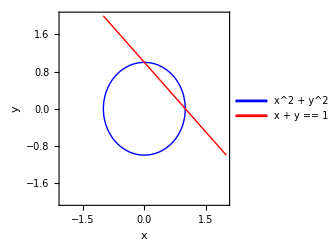

{{1.,0.},{0.,1.}}

-Graphics3D-

```mathematica
(*Define equations*)
eq1=x^2+y^2==1;
eq2=x+y==1;

(*Plot both equations*)
ContourPlot[{x^2+y^2==1,x+y==1},{x,-2,2},{y,-2,2},ContourStyle->{Directive[Blue,Thick],Directive[Red,Thick]},PlotLegends->{"x^2 + y^2 == 1","x + y == 1"},AxesLabel->{"x","y"},PlotRange->{{-2,2},{-2,2}}]

(*Find intersection points*)
intersections={x,y}/. NSolve[{x^2+y^2==1,x+y==1},{x,y}]

(*Define your equation*)
equation=x^2+y^2;

(*Plot the equation*)
Plot3D[equation,{x,-5,5},{y,-5,5},AxesLabel->{"x","y","z"},PlotLabel->"Plot of the equation z = x^2 + y^2"]
```